```mathematica
R[th_]:={{Cos[th],Sin[th]},{-Sin[th],Cos[th]}}
```

```mathematica
R[th]//MatrixForm
```

(Cos[th] | Sin[th]
-Sin[th] | Cos[th])

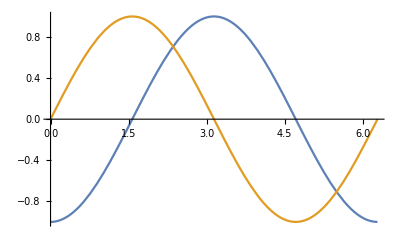

```mathematica
Plot[{
(R[x].{{-1},{0}})[[1]],
(R[x].{{-1},{0}})[[2]]
}
,{x,0,2π}]
```

```mathematica
Eigenvectors[R[th]]
```

{{-ⅈ,1},{ⅈ,1}}

### Define Rotation matrices and measurements

```mathematica
R2[th_]:={
{Cos[th],Sin[th], 0 , 0},
{-Sin[th],Cos[th], 0, 0},
{0,0,Cos[th],Sin[th]},
{0,0,-Sin[th],Cos[th]}
};
R1[th_]:={
{Cos[th],0, Sin[th], 0},
{0,Cos[th], 0, Sin[th]},
{-Sin[th],0,Cos[th],0},
{0,-Sin[th],0,Cos[th]}
};
Z1={
{1,0,0,0},
{0,1,0,0},
{0,0,-1,0},
{0,0,0,-1}
};
Z2={
{1,0,0,0},
{0,-1,0,0},
{0,0,1,0},
{0,0,0,-1}
};
```

### Fix rotation angles

```mathematica
a1=π/2;
a2=0;
b1=π/2;
b2=0;
```

{{0,0,0,0},{0,1/2,0,0},{0,0,1/2,0},{0,0,0,0}}

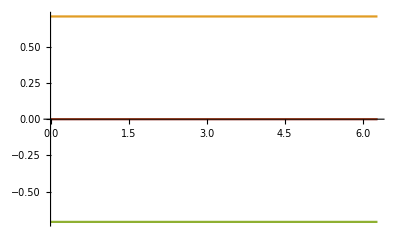

```mathematica
vinit={{1/√2},{0},{0},{1/√2}};
vinit={{0},{1/√2},{-1/√2},{0}};
rhoInit=vinit.Transpose[vinit];
rhoMix=DiagonalMatrix[Diagonal[rhoInit]]
Plot[{
(R1[x].R2[x].vinit)⟦1⟧,
(R1[x].R2[x].vinit)⟦2⟧,
(R1[x].R2[x].vinit)⟦3⟧,
(R1[x].R2[x].vinit)⟦4⟧
},
{x,0,2π}
]
```

```mathematica
zz=Tr[Z1.Z2.rhoInit]
Ra1b1=R1[a1].R2[b1];
Va1b1=Ra1b1.vinit;
Roa1b1 = Va1b1.Transpose[Va1b1];

Ra1b2=R1[a1].R2[b2];
Va1b2=Ra1b2.vinit;
Roa1b2 = Va1b2.Transpose[Va1b2];

Ra2b1=R1[a2].R2[b1];
Va2b1=Ra2b1.vinit;
Roa2b1 = Va2b1.Transpose[Va2b1];

Ra2b2=R1[a2].R2[b2];
Va2b2=Ra2b2.vinit;
Roa2b2 = Va2b2.Transpose[Va2b2];

Ea1b1 = Tr[Z1.Z2.Roa1b1];
Ea1b2 = Tr[Z1.Z2.Roa1b2];
Ea2b1 = Tr[Z1.Z2.Roa2b1];
Ea2b2 = Tr[Z1.Z2.Roa2b2];

ERaRb[a0_,b0_]:=
Module[{a=a0,b=b0},
Rab=R1[a].R2[b];
Rhoab=Rab.rhoInit.Transpose[Rab];
Tr[-Z1.Z2.Rhoab]
]


ERaRbMix[a0_,b0_]:=
Module[{a=a0,b=b0},
Rab=R1[a].R2[b];
Rhoab=Rab.rhoMix.Transpose[Rab];
Tr[-Z1.Z2.Rhoab]
]

Manipulate[
Plot[{
ERaRb[a,b]-ERaRb[a,b+d π 2]+ERaRb[a+d π 2,b]+ERaRb[a+d π 2,b+d π 2],
ERaRbMix[a,b]-ERaRbMix[a,b+d π 2]+ERaRbMix[a+d π 2,b]+ERaRbMix[a+d π 2,b+d π 2]
},{b,0,2 π},
PlotRange-> {{0,π},{-2 √2,2 √2}}
]
,{a,0,2π}
,{d,0,1}
]
(*
Diagonal[Roa1b1]
Diagonal[Roa1b2]
Diagonal[Roa2b1]
Diagonal[Roa2b2]
*)
```

-1

```mathematica
N[1/8]
```

0.125

```mathematica
ERaRb[π/2,0]
```

1

```mathematica
Vab=Rab.vinit;
Rhoab = Vab.Transpose[Vab];
```

```mathematica
rhoInit
```

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}

```mathematica
Diagonal[rhoInit]
```

{0,1/2,1/2,0}

{{0,0,0,0},{0,1/2,0,0},{0,0,1/2,0},{0,0,0,0}}

```mathematica
rhoMix
```

{{0,0,0,0},{0,1/2,0,0},{0,0,1/2,0},{0,0,0,0}}

```mathematica
rhoInit
```

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}